```mathematica
(*Compute the repo root from the notebook location*)
repoRoot=ParentDirectory@NotebookDirectory[];
repoAppDir=FileNameJoin[{repoRoot,"mma"}];
repoExternDir=FileNameJoin[{repoRoot,"mma","extern"}];

If[!MemberQ[$Path,repoAppDir],AppendTo[$Path,repoAppDir];];
If[!MemberQ[$Path,repoExternDir],AppendTo[$Path,repoExternDir];];

ClearAll["LocalF1`*"];
<<LocalF1`;

ClearAll["CoulombHiggs`*"];
<<CoulombHiggs`;
```

CoulombHiggs 6.3 - A package for evaluating quiver invariants

## Examples at m = -1/10

Adding 162 rays,

Adding 842 rays,

Adding 921 rays,

Adding 137 rays,

Adding 2 rays,

2088 in total.

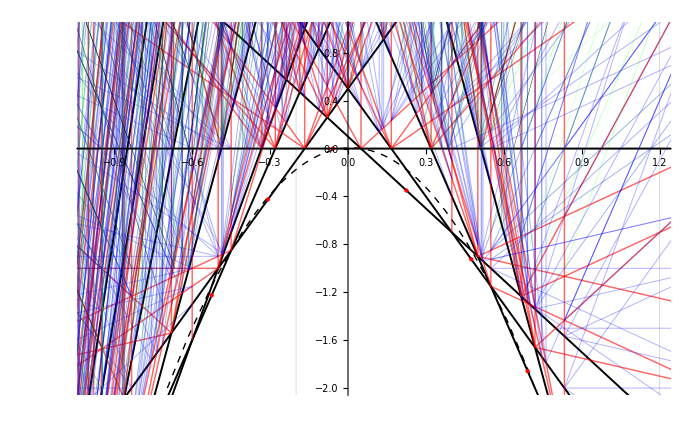

```mathematica
With[{mu=-1/10, L=4,len=20},
InitialRays=InitialRaysFromColl[CollInitial[[3]]/.repCh, -2,1,mu];
ListRays=ConstructLVDiagramOpt[13,4,mu,InitialRays];

Show[
Plot[XYParabolaY[x,mu,0,0],{x,-2,2},
PlotRange->{{-1,1.2},{-2,1}},
PlotStyle->Directive[Dashed,Thick,Black],
GridLines->{{-0.2,1.2},None}
],
(*Graphics[{Opacity[.25],ConstructDomain[#, mu,L]&/@CollPlotData}],*)
Graphics[{
Tooltip[XYRaySegment[#,mu,len,RayStyleMap], #[[1]]]&/@ListRays,    (*rays*)
PointSize[.004],Red,
Point[#[[2]]&/@InitialRays]                   (*initial positions*)
}]
]
]
```

```mathematica
ObjectsToCheckHC={
{0,0,1,1/2},
{0,1,-1,0},
{0,1,0,1/2},
{0,2,-1,1/2},
{0,2,0,0},
{0,3,-1,0},
{0,3,0,1/2},
{0,4,-2,0},
{1,2,0,x},
{1,0,1,x},
{1,1,1,x},
{1,2,1,x},
-{1,0,-1,x},
-{1,2,-1,x},
{1,0,0,-1},
{1,0,0,-2},
{2,1,0,-1/2},
{2,1,-1,-1}
};
```

```mathematica
ToFB/@ObjectsToCheckHC;
ObjectsToCheck=Table[If[FreeQ[gam, x], gam, gam/.First[Solve[BogomolovDiscriminant[gam]==0,x]]], {gam, %}]
```

{{0,0,1,1/2},{0,1,0,0},{0,1,1,1/2},{0,2,1,1/2},{0,2,2,0},{0,3,2,0},{0,3,3,1/2},{0,4,2,0},{1,2,2,2},{1,0,1,-1/2},{1,1,2,0},{1,2,3,3/2},{-1,0,1,1/2},{-1,-2,-1,-3/2},{1,0,0,-1},{1,0,0,-2},{2,1,1,-1/2},{2,1,0,-1}}

```mathematica
LVTreesFromListRays[ListRays,{0,0,1,1/2},-1/10]
ScattIndexImproved[%]
```

{{{-1,-1,0,0},{1,1,1,1/2}}}

{1}

```mathematica
LVTreesFromListRays[ListRays,{0,1,0,0},-1/10]
ScattIndexImproved[%]
```

{{{-1,0,0,0},{1,1,0,0}}}

{-(1+y^2)/y}

```mathematica
LVTreesFromListRays[ListRays,{0,1,1,1/2},-1/10]
ScattIndexImproved[%]
```

{{{-1,0,0,0},{1,1,1,1/2}}}

{1+1/y^2+y^2}

```mathematica
LVTreesFromListRays[ListRays,{0,2,1,1/2},-1/10]
ScattIndexImproved[%]
```

{{{1,1,1,1/2},{{-2,0,0,0},{1,1,0,0}}}}

{1+1/y^4+1/y^2+y^2+y^4}

```mathematica
LVTreesFromListRays[ListRays,{0,2,2,0},-1/10]
ScattIndexImproved[%]
Series[%[[1]],{y,Infinity,20}]
```

{{{1,1,1,1/2},{-1,1,1,-1/2}}}

{(1-y^12)/(y^5 (-1+y^2))}

-y^5-y^3-y-1/y-(1/y)^3-(1/y)^5+O[1/y]^21

```mathematica
ToHC/@{{1,1,1,1/2},{-1,1,1,-1/2}}
```

{{1,1,0,1/2},{-1,1,0,-1/2}}

```mathematica
LVTreesFromListRays[ListRays,{0,3,2,0},-1/10]
ScattIndexImproved[%]
Series[%[[1]],{y,Infinity,20}]
```

No such dimension vector in the list

{}

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
LVTreesFromListRays[ListRays,{0,3,3,0},-1/10]
ScattIndexImproved[%]
Series[%[[1]],{y,Infinity,20}]
```

No such dimension vector in the list

{}

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
LVTreesFromListRays[ListRays,{0,4,2,0},-1/10]
ScattIndexImproved[%]
Series[%[[1]],{y,Infinity,100}]
```

{{{-1,2,1,-3/2},{1,2,1,3/2}}}

{-(-1+y^20)/(y^9 (-1+y^2))}

-y^9-y^7-y^5-y^3-y-1/y-(1/y)^3-(1/y)^5-(1/y)^7-(1/y)^9+O[1/y]^101

```mathematica
ToHC/@{{-1,2,1,-3/2},{1,2,1,3/2}}
```

{{-1,2,-1,-3/2},{1,2,-1,3/2}}

```mathematica
-{1,-2,1,x}+{1,2,-1,y}
```

{0,4,-2,-x+y}

```mathematica
LVTreesFromListRays[ListRays,{1,2,2,2},-1/10]
ScattIndexImproved[%]
Series[%[[1]],{y,Infinity,100}]
```

{{{1,2,1,3/2},{{-1,-1,0,0},{1,1,1,1/2}}}}

{1}

1

```mathematica
ToHC@{1,2,1,3/2}
```

{1,2,-1,3/2}

```mathematica
LVTreesFromListRays[ListRays,{1,0,1,-1/2},-1/10]
ScattIndexImproved[%]
Series[%[[1]],{y,Infinity,100}]
```

{{{1,0,0,0},{{-1,2,2,-2},{1,-2,-1,3/2}}}}

{1}

1

```mathematica
ToHC@{1,0,0,0}
```

{1,0,0,0}

```mathematica
LVTreesFromListRays[ListRays,{1,1,2,0},-1/10]
ScattIndexImproved[%]
Series[%[[1]],{y,Infinity,100}]
```

{{{1,1,1,1/2},{{-1,2,2,-2},{1,-2,-1,3/2}}}}

{1}

1

```mathematica
ToHC/@{{1,1,1,1/2}}
```

{{1,1,0,1/2}}

```mathematica
LVTreesFromListRays[ListRays,{1,2,3,3/2},-1/10]
ScattIndexImproved[%]
Series[%[[1]],{y,Infinity,100}]
```

No such dimension vector in the list

{}

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
LVTreesFromListRays[ListRays,{-1,0,1,1/2},-1/10]
ScattIndexImproved[%]
Series[%[[1]],{y,Infinity,100}]
```

{{{-1,0,0,0},{{-1,-1,0,0},{1,1,1,1/2}}}}

{1}

1

```mathematica
ToHC/@{{-1,-1,0,0},{1,1,1,1/2}}
```

{{-1,-1,1,0},{1,1,0,1/2}}

```mathematica
LVTreesFromListRays[ListRays,{-1,-2,-1,-3/2},-1/10]
ScattIndexImproved[%]
Series[%[[1]],{y,Infinity,100}]
```

{{-1,-2,-1,-3/2}}

{1}

1

```mathematica
-ToFB[-{1,2,-1,x}]
```

{1,2,1,x}

```mathematica
{{{Ch[-2,-2][1],2 Ch[-1,-1]}}, {{{Ch[-2,-2][1],Ch[-2,-1]},{Ch[-2,-1][1],2 Ch[-1,-1]}}}}
```

```mathematica
LVTreesFromListRays[ListRays,{1,0,0,-1},-1/10]
{ChernToCh[%](*/.{Ch[p_,q_]:>ChHC[p,-p+q]}*),ScattIndexImproved[%,y]}
Series[Total[%[[2]]],{y,Infinity,100}]
```

{{{-1,2,2,-2},{2,-2,-2,1}},{{{-1,2,2,-2},{1,-2,-1,3/2}},{{-1,2,1,-3/2},{2,-2,-2,1}}}}

{{{Ch[-2,-2][1],2 Ch[-1,-1]},{{Ch[-2,-2][1],Ch[-2,-1]},{Ch[-2,-1][1],2 Ch[-1,-1]}}},{1+1/y^2+y^2,1}}

y^2+2+(1/y)^2+O[1/y]^101

```mathematica
temp=LVTreesFromListRays[ListRays,{1,0,0,-2},-1/10]
{ChernToCh[%]/.{Ch[p_,q_]:>ChHC[p,-p+q]},ScattIndexImproved[%]}
Series[%[[2,1]],{y,Infinity,100}]
```

{{{1,-1,-1,1/2},{{-1,3,2,-4},{1,-2,-1,3/2}}},{{{-1,5,4,-12},{1,-5,-3,21/2}},{{-1,2,1,-3/2},{2,-2,-2,1}}}}

{{{ChHC[-1,0],{ChHC[-3,1][1],ChHC[-2,1]}},{{ChHC[-5,1][1],ChHC[-5,2]},{ChHC[-2,1][1],2 ChHC[-1,0]}}},{((1+y^2+y^4)^2)/y^4,1}}

y^4+2 y^2+3+2/y^2+(1/y)^4+O[1/y]^101

```mathematica
temp=LVTreesFromListRays[ListRays,{2,1,1,-1/2},-1/10]
{ChernToCh[%]/.{Ch[p_,q_]:>ChHC[p,-p+q]},ScattIndexImproved[%]}
Series[%[[2,1]],{y,Infinity,100}]
```

{{{3,0,0,0},{-1,1,1,-1/2}}}

{{{3 ChHC[0,0],ChHC[-1,0][1]}},{1}}

1

```mathematica
temp=LVTreesFromListRays[ListRays,{2,1,0,-1},-1/10]
{ChernToCh[%]/.{Ch[p_,q_]:>ChHC[p,-p+q]},ScattIndexImproved[%]}
Series[%[[2,1]],{y,Infinity,100}]
```

{{{2,0,0,0},{{-1,2,1,-3/2},{1,-1,-1,1/2}}}}

{{{2 ChHC[0,0],{ChHC[-2,1][1],ChHC[-1,0]}}},{-(1+y^2)/y}}

-y-1/y+O[1/y]^101

```mathematica
indexTable=Table[
temp=LVTreesFromListRays[ListRays,gam,-1/10];
{ToHC[gam],gam, Column[ChernToCh[temp]], Column[ChernToCh[temp]/.{Ch[p_,q_]:>ChHC[p,-p+q]}], Series[Total[ScattIndexImproved[temp, y]], {y,Infinity,100}]},
 {gam, ObjectsToCheck}];
```

```mathematica
Grid[Prepend[indexTable[[All,{2,1,3,5}]], {"charge in FB basis","charge in HC basis (previous notation)", "contributing trees", "index"}],Frame->All]
```

charge in FB basis | charge in HC basis (previous notation) | contributing trees | index
{0,0,1,1/2} | {0,0,1,1/2} | {Ch[1,0][1],Ch[1,1]} | 1
{0,1,0,0} | {0,1,-1,0} | {Ch[0,0][1],Ch[1,0]} | -y-1/y+O[1/y]^101
{0,1,1,1/2} | {0,1,0,1/2} | {Ch[0,0][1],Ch[1,1]} | y^2+1+(1/y)^2+O[1/y]^101
{0,2,1,1/2} | {0,2,-1,1/2} | {Ch[1,1],{2 Ch[0,0][1],Ch[1,0]}} | y^4+y^2+1+(1/y)^2+(1/y)^4+O[1/y]^101
{0,2,2,0} | {0,2,0,0} | {Ch[1,1],Ch[-1,-1][1]} | -y^5-y^3-y-1/y-(1/y)^3-(1/y)^5+O[1/y]^101
{0,3,2,0} | {0,3,-1,0} | {Ch[-1,-1][1],{Ch[1,1],{Ch[0,0][1],Ch[1,0]}}} | -y^9-3 y^7-4 y^5-4 y^3-4 y-4/y-4/y^3-4/y^5-3/y^7-(1/y)^9+O[1/y]^101
{0,3,3,1/2} | {0,3,0,1/2} | {Ch[-1,-1][1],{Ch[0,0][1],2 Ch[1,1]}} | y^10+2 y^8+3 y^6+3 y^4+3 y^2+3+3/y^2+3/y^4+3/y^6+2/y^8+(1/y)^10+O[1/y]^101
{0,4,2,0} | {0,4,-2,0} | {Ch[-2,-1][1],Ch[2,1]}
{Ch[-1,-1][1],{Ch[1,1],{2 Ch[0,0][1],2 Ch[1,0]}}} | -y^13-3 y^11-8 y^9-10 y^7-11 y^5-11 y^3-11 y-11/y-11/y^3-11/y^5-10/y^7-8/y^9-3/y^11-(1/y)^13+O[1/y]^101
{1,2,2,2} | {1,2,0,2} | {Ch[2,1],{Ch[1,0][1],Ch[1,1]}} | 1
{1,0,1,-1/2} | {1,0,1,-1/2} | {Ch[0,0],{Ch[-2,-2][1],Ch[-2,-1]}} | 1
{1,1,2,0} | {1,1,1,0} | {Ch[1,1],{Ch[-2,-2][1],Ch[-2,-1]}} | 1
{1,2,3,3/2} | {1,2,1,3/2} | {{Ch[-2,-2][1],Ch[-2,-1]},{Ch[2,1],{Ch[1,0][1],Ch[1,1]}}} | 1
{-1,0,1,1/2} | {-1,0,1,1/2} | {Ch[0,0][1],{Ch[1,0][1],Ch[1,1]}} | 1
{-1,-2,-1,-3/2} | {-1,-2,1,-3/2} | Ch[2,1][1] | 1
{1,0,0,-1} | {1,0,0,-1} | {Ch[-2,-2][1],2 Ch[-1,-1]}
{{Ch[-2,-2][1],Ch[-2,-1]},{Ch[-2,-1][1],2 Ch[-1,-1]}} | y^2+2+(1/y)^2+O[1/y]^101
{1,0,0,-2} | {1,0,0,-2} | {Ch[-1,-1],{Ch[-3,-2][1],Ch[-2,-1]}}
{{Ch[-5,-4][1],Ch[-5,-3]},{Ch[-2,-1][1],2 Ch[-1,-1]}}
{{Ch[-3,-2][1],Ch[-2,-2]},{Ch[-1,-1],{Ch[-2,-2][1],Ch[-2,-1]}}} | y^4+3 y^2+6+3/y^2+(1/y)^4+O[1/y]^101
{2,1,1,-1/2} | {2,1,0,-1/2} | {3 Ch[0,0],Ch[-1,-1][1]} | 1
{2,1,0,-1} | {2,1,-1,-1} | {2 Ch[0,0],{Ch[-2,-1][1],Ch[-1,-1]}} | -y-1/y+O[1/y]^101

```mathematica
Grid[Prepend[indexTable, {"gam in HC", "gam in FB", "Trees", "Trees in HC", "Improved Index"}],Frame->All]
```

gam in HC | gam in FB | Trees | Trees in HC | Improved Index
{0,0,1,1/2} | {0,0,1,1/2} | {Ch[1,0][1],Ch[1,1]} | {ChHC[1,-1][1],ChHC[1,0]} | 1
{0,1,-1,0} | {0,1,0,0} | {Ch[0,0][1],Ch[1,0]} | {ChHC[0,0][1],ChHC[1,-1]} | -y-1/y+O[1/y]^101
{0,1,0,1/2} | {0,1,1,1/2} | {Ch[0,0][1],Ch[1,1]} | {ChHC[0,0][1],ChHC[1,0]} | y^2+1+(1/y)^2+O[1/y]^101
{0,2,-1,1/2} | {0,2,1,1/2} | {Ch[1,1],{2 Ch[0,0][1],Ch[1,0]}} | {ChHC[1,0],{2 ChHC[0,0][1],ChHC[1,-1]}} | y^4+y^2+1+(1/y)^2+(1/y)^4+O[1/y]^101
{0,2,0,0} | {0,2,2,0} | {Ch[1,1],Ch[-1,-1][1]} | {ChHC[1,0],ChHC[-1,0][1]} | -y^5-y^3-y-1/y-(1/y)^3-(1/y)^5+O[1/y]^101
{0,3,-1,0} | {0,3,2,0} | {Ch[-1,-1][1],{Ch[1,1],{Ch[0,0][1],Ch[1,0]}}} | {ChHC[-1,0][1],{ChHC[1,0],{ChHC[0,0][1],ChHC[1,-1]}}} | -y^9-3 y^7-4 y^5-4 y^3-4 y-4/y-4/y^3-4/y^5-3/y^7-(1/y)^9+O[1/y]^101
{0,3,0,1/2} | {0,3,3,1/2} | {Ch[-1,-1][1],{Ch[0,0][1],2 Ch[1,1]}} | {ChHC[-1,0][1],{ChHC[0,0][1],2 ChHC[1,0]}} | y^10+2 y^8+3 y^6+3 y^4+3 y^2+3+3/y^2+3/y^4+3/y^6+2/y^8+(1/y)^10+O[1/y]^101
{0,4,-2,0} | {0,4,2,0} | {Ch[-2,-1][1],Ch[2,1]}
{Ch[-1,-1][1],{Ch[1,1],{2 Ch[0,0][1],2 Ch[1,0]}}} | {ChHC[-2,1][1],ChHC[2,-1]}
{ChHC[-1,0][1],{ChHC[1,0],{2 ChHC[0,0][1],2 ChHC[1,-1]}}} | -y^13-3 y^11-8 y^9-10 y^7-11 y^5-11 y^3-11 y-11/y-11/y^3-11/y^5-10/y^7-8/y^9-3/y^11-(1/y)^13+O[1/y]^101
{1,2,0,2} | {1,2,2,2} | {Ch[2,1],{Ch[1,0][1],Ch[1,1]}} | {ChHC[2,-1],{ChHC[1,-1][1],ChHC[1,0]}} | 1
{1,0,1,-1/2} | {1,0,1,-1/2} | {Ch[0,0],{Ch[-2,-2][1],Ch[-2,-1]}} | {ChHC[0,0],{ChHC[-2,0][1],ChHC[-2,1]}} | 1
{1,1,1,0} | {1,1,2,0} | {Ch[1,1],{Ch[-2,-2][1],Ch[-2,-1]}} | {ChHC[1,0],{ChHC[-2,0][1],ChHC[-2,1]}} | 1
{1,2,1,3/2} | {1,2,3,3/2} | {{Ch[-2,-2][1],Ch[-2,-1]},{Ch[2,1],{Ch[1,0][1],Ch[1,1]}}} | {{ChHC[-2,0][1],ChHC[-2,1]},{ChHC[2,-1],{ChHC[1,-1][1],ChHC[1,0]}}} | 1
{-1,0,1,1/2} | {-1,0,1,1/2} | {Ch[0,0][1],{Ch[1,0][1],Ch[1,1]}} | {ChHC[0,0][1],{ChHC[1,-1][1],ChHC[1,0]}} | 1
{-1,-2,1,-3/2} | {-1,-2,-1,-3/2} | Ch[2,1][1] | ChHC[2,-1][1] | 1
{1,0,0,-1} | {1,0,0,-1} | {Ch[-2,-2][1],2 Ch[-1,-1]}
{{Ch[-2,-2][1],Ch[-2,-1]},{Ch[-2,-1][1],2 Ch[-1,-1]}} | {ChHC[-2,0][1],2 ChHC[-1,0]}
{{ChHC[-2,0][1],ChHC[-2,1]},{ChHC[-2,1][1],2 ChHC[-1,0]}} | y^2+2+(1/y)^2+O[1/y]^101
{1,0,0,-2} | {1,0,0,-2} | {Ch[-1,-1],{Ch[-3,-2][1],Ch[-2,-1]}}
{{Ch[-5,-4][1],Ch[-5,-3]},{Ch[-2,-1][1],2 Ch[-1,-1]}}
{{Ch[-3,-2][1],Ch[-2,-2]},{Ch[-1,-1],{Ch[-2,-2][1],Ch[-2,-1]}}} | {ChHC[-1,0],{ChHC[-3,1][1],ChHC[-2,1]}}
{{ChHC[-5,1][1],ChHC[-5,2]},{ChHC[-2,1][1],2 ChHC[-1,0]}}
{{ChHC[-3,1][1],ChHC[-2,0]},{ChHC[-1,0],{ChHC[-2,0][1],ChHC[-2,1]}}} | y^4+3 y^2+6+3/y^2+(1/y)^4+O[1/y]^101
{2,1,0,-1/2} | {2,1,1,-1/2} | {3 Ch[0,0],Ch[-1,-1][1]} | {3 ChHC[0,0],ChHC[-1,0][1]} | 1
{2,1,-1,-1} | {2,1,0,-1} | {2 Ch[0,0],{Ch[-2,-1][1],Ch[-1,-1]}} | {2 ChHC[0,0],{ChHC[-2,1][1],ChHC[-1,0]}} | -y-1/y+O[1/y]^101

```mathematica
InitialPosition[{0,3,3,0}]
```

Non integer second Chern class !

0

```mathematica
SecondChernClass@ToFB[{0,3,0,0}]
```

9/2

```mathematica
Expand[1/2(dH H+dC C)^2-ch2]/.{H^2->1,C^2->-1,H C->0}
%/.Thread[{r,dH,dC,ch2}->{0,3,0,0}]
```

-ch2-dC^2/2+dH^2/2

9/2

```mathematica
indexTable2=Table[
temp=LVTreesFromListRays[ListRays,gam,-1/10];
{ToHC[gam],gam, Column[ChernToCh[temp]], Column[ChernToCh[temp]/.{Ch[p_,q_]:>ChHC[p,-p+q]}], Series[Total[ScattIndexImproved[temp, y]], {y,Infinity,100}]},
 {gam, Select[ListRays[[All,1]],#[[1;;3]]=={0,3,3}&]}];
Grid[Prepend[indexTable2, {"gam in HC", "gam in FB", "Trees", "Trees in HC", "Improved Index"}],Frame->All]
```

Non integer second Chern class !

Non integer second Chern class !

Non integer second Chern class !

«13 more identical outputs»

gam in HC | gam in FB | Trees | Trees in HC | Improved Index
{0,3,0,-21/2} | {0,3,3,-21/2} | {{-1/3,5/3,4/3,-4},{1/3,-2/3,-1/3,1/2}}
{Ch[-3,-2],Ch[-4,-3][1]} | {{-1/3,5/3,4/3,-4},{1/3,-2/3,-1/3,1/2}}
{ChHC[-3,1],ChHC[-4,1][1]} | y^2+1+(1/y)^2+O[1/y]^101
{0,3,0,-3/2} | {0,3,3,-3/2} | {{-1/3,2/3,2/3,-2/3},{1/3,1/3,1/3,1/6}}
{Ch[0,0],Ch[-1,-1][1]} | {{-1/3,2/3,2/3,-2/3},{1/3,1/3,1/3,1/6}}
{ChHC[0,0],ChHC[-1,0][1]} | y^2+1+(1/y)^2+O[1/y]^101
{0,3,0,-25/2} | {0,3,3,-25/2} | {Ch[-3,-2],{2 Ch[-5,-4][1],Ch[-4,-3]}} | {ChHC[-3,1],{2 ChHC[-5,1][1],ChHC[-4,1]}} | y^10+2 y^8+3 y^6+3 y^4+3 y^2+3+3/y^2+3/y^4+3/y^6+2/y^8+(1/y)^10+O[1/y]^101
{0,3,0,-7/2} | {0,3,3,-7/2} | {Ch[0,0],{2 Ch[-2,-2][1],Ch[-1,-1]}} | {ChHC[0,0],{2 ChHC[-2,0][1],ChHC[-1,0]}} | y^10+2 y^8+3 y^6+3 y^4+3 y^2+3+3/y^2+3/y^4+3/y^6+2/y^8+(1/y)^10+O[1/y]^101
{0,3,0,11/2} | {0,3,3,11/2} | {Ch[3,2],{2 Ch[1,0][1],Ch[2,1]}} | {ChHC[3,-1],{2 ChHC[1,-1][1],ChHC[2,-1]}} | y^10+2 y^8+3 y^6+3 y^4+3 y^2+3+3/y^2+3/y^4+3/y^6+2/y^8+(1/y)^10+O[1/y]^101
{0,3,0,-23/2} | {0,3,3,-23/2} | {Ch[-5,-4][1],{2 Ch[-3,-2],Ch[-4,-3][1]}} | {ChHC[-5,1][1],{2 ChHC[-3,1],ChHC[-4,1][1]}} | y^10+2 y^8+3 y^6+3 y^4+3 y^2+3+3/y^2+3/y^4+3/y^6+2/y^8+(1/y)^10+O[1/y]^101
{0,3,0,-5/2} | {0,3,3,-5/2} | {Ch[-2,-2][1],{2 Ch[0,0],Ch[-1,-1][1]}} | {ChHC[-2,0][1],{2 ChHC[0,0],ChHC[-1,0][1]}} | y^10+2 y^8+3 y^6+3 y^4+3 y^2+3+3/y^2+3/y^4+3/y^6+2/y^8+(1/y)^10+O[1/y]^101
{0,3,0,13/2} | {0,3,3,13/2} | {Ch[1,0][1],{2 Ch[3,2],Ch[2,1][1]}} | {ChHC[1,-1][1],{2 ChHC[3,-1],ChHC[2,-1][1]}} | y^10+2 y^8+3 y^6+3 y^4+3 y^2+3+3/y^2+3/y^4+3/y^6+2/y^8+(1/y)^10+O[1/y]^101
{0,3,0,-19/2} | {0,3,3,-19/2} | {Ch[-2,-1],{Ch[-3,-2],2 Ch[-4,-3][1]}} | {ChHC[-2,1],{ChHC[-3,1],2 ChHC[-4,1][1]}} | y^10+2 y^8+3 y^6+3 y^4+3 y^2+3+3/y^2+3/y^4+3/y^6+2/y^8+(1/y)^10+O[1/y]^101
{0,3,0,-1/2} | {0,3,3,-1/2} | {Ch[1,1],{Ch[0,0],2 Ch[-1,-1][1]}} | {ChHC[1,0],{ChHC[0,0],2 ChHC[-1,0][1]}} | y^10+2 y^8+3 y^6+3 y^4+3 y^2+3+3/y^2+3/y^4+3/y^6+2/y^8+(1/y)^10+O[1/y]^101
{0,3,0,-17/2} | {0,3,3,-17/2} | {Ch[-4,-3][1],{Ch[-3,-2][1],2 Ch[-2,-1]}} | {ChHC[-4,1][1],{ChHC[-3,1][1],2 ChHC[-2,1]}} | y^10+2 y^8+3 y^6+3 y^4+3 y^2+3+3/y^2+3/y^4+3/y^6+2/y^8+(1/y)^10+O[1/y]^101
{0,3,0,1/2} | {0,3,3,1/2} | {Ch[-1,-1][1],{Ch[0,0][1],2 Ch[1,1]}} | {ChHC[-1,0][1],{ChHC[0,0][1],2 ChHC[1,0]}} | y^10+2 y^8+3 y^6+3 y^4+3 y^2+3+3/y^2+3/y^4+3/y^6+2/y^8+(1/y)^10+O[1/y]^101
{0,3,0,-11/2} | {0,3,3,-11/2} | {Ch[-3,-2][1],{{Ch[-2,-2][1],Ch[-2,-1]},{Ch[-2,-2][1],2 Ch[-1,-1]}}} | {ChHC[-3,1][1],{{ChHC[-2,0][1],ChHC[-2,1]},{ChHC[-2,0][1],2 ChHC[-1,0]}}} | y^10+2 y^8+3 y^6+3 y^4+3 y^2+3+3/y^2+3/y^4+3/y^6+2/y^8+(1/y)^10+O[1/y]^101
{0,3,0,7/2} | {0,3,3,7/2} | {Ch[0,0][1],{{Ch[1,0][1],Ch[1,1]},{Ch[1,0][1],2 Ch[2,1]}}} | {ChHC[0,0][1],{{ChHC[1,-1][1],ChHC[1,0]},{ChHC[1,-1][1],2 ChHC[2,-1]}}} | y^10+2 y^8+3 y^6+3 y^4+3 y^2+3+3/y^2+3/y^4+3/y^6+2/y^8+(1/y)^10+O[1/y]^101
{0,3,0,-9/2} | {0,3,3,-9/2} | {Ch[-2,-2][1],Ch[-1,-1]}
{{1/3,0,0,0},{{-1/3,1,2/3,-4/3},{{-1/3,2/3,2/3,-2/3},{1/3,-2/3,-1/3,1/2}}}} | {ChHC[-2,0][1],ChHC[-1,0]}
{{1/3,0,0,0},{{-1/3,1,2/3,-4/3},{{-1/3,2/3,2/3,-2/3},{1/3,-2/3,-1/3,1/2}}}} | y^2+1+(1/y)^2+O[1/y]^101
{0,3,0,9/2} | {0,3,3,9/2} | {Ch[1,0][1],Ch[2,1]}
{{1/3,1,2/3,4/3},{{-1/3,0,0,0},{{-1/3,-1/3,0,0},{1/3,1/3,1/3,1/6}}}} | {ChHC[1,-1][1],ChHC[2,-1]}
{{1/3,1,2/3,4/3},{{-1/3,0,0,0},{{-1/3,-1/3,0,0},{1/3,1/3,1/3,1/6}}}} | y^2+1+(1/y)^2+O[1/y]^101
{0,3,0,-15/2} | {0,3,3,-15/2} | {Ch[-3,-2][1],Ch[-2,-1]}
{{-1/3,4/3,1,-5/2},{{1/3,-1/3,-1/3,1/6},{{-1/3,2/3,2/3,-2/3},{1/3,-2/3,-1/3,1/2}}}} | {ChHC[-3,1][1],ChHC[-2,1]}
{{-1/3,4/3,1,-5/2},{{1/3,-1/3,-1/3,1/6},{{-1/3,2/3,2/3,-2/3},{1/3,-2/3,-1/3,1/2}}}} | y^2+1+(1/y)^2+O[1/y]^101
{0,3,0,3/2} | {0,3,3,3/2} | {Ch[0,0][1],Ch[1,1]}
{{-1/3,1/3,1/3,-1/6},{{1/3,2/3,1/3,1/2},{{-1/3,-1/3,0,0},{1/3,1/3,1/3,1/6}}}} | {ChHC[0,0][1],ChHC[1,0]}
{{-1/3,1/3,1/3,-1/6},{{1/3,2/3,1/3,1/2},{{-1/3,-1/3,0,0},{1/3,1/3,1/3,1/6}}}} | y^2+1+(1/y)^2+O[1/y]^101
{0,3,0,-13/2} | {0,3,3,-13/2} | {{2 Ch[-3,-2][1],Ch[-2,-1]},{Ch[-1,-1],{Ch[-2,-2][1],Ch[-2,-1]}}} | {{2 ChHC[-3,1][1],ChHC[-2,1]},{ChHC[-1,0],{ChHC[-2,0][1],ChHC[-2,1]}}} | y^10+2 y^8+3 y^6+3 y^4+3 y^2+3+3/y^2+3/y^4+3/y^6+2/y^8+(1/y)^10+O[1/y]^101
{0,3,0,5/2} | {0,3,3,5/2} | {{2 Ch[0,0][1],Ch[1,1]},{Ch[2,1],{Ch[1,0][1],Ch[1,1]}}} | {{2 ChHC[0,0][1],ChHC[1,0]},{ChHC[2,-1],{ChHC[1,-1][1],ChHC[1,0]}}} | y^10+2 y^8+3 y^6+3 y^4+3 y^2+3+3/y^2+3/y^4+3/y^6+2/y^8+(1/y)^10+O[1/y]^101

```mathematica
ExpandWithParents[rays_,list_:ListRays]:=
Module[{ids0,ids},
ids0=Union@DeleteCases[Flatten@rays[[All,{3,4}]],0];
ids=FixedPoint[Union@Join[#,DeleteCases[Flatten@list[[#,{3,4}]],0]]&,ids0];
DeleteDuplicates@Join[rays,Select[list[[ids]],#[[{3,4}]]=!={0,0}&]]
]
```

```mathematica
ExampleRays=Select[ListRays, MemberQ[ObjectsToCheck,#[[1]]]&];
ExpandedRays=ExpandWithParents[ExampleRays];
```

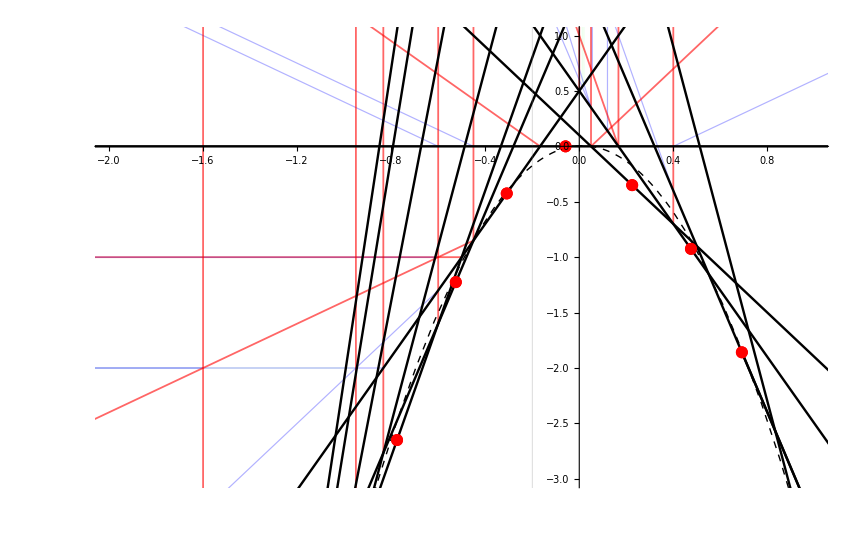

```mathematica
plt=With[{mu=-1/10, L=4,len=20},
Show[
Plot[XYParabolaY[x,mu,0,0],{x,-2,2},
PlotRange->{{-15,15},{-15,15}},
PlotStyle->Directive[Dashed,Thick,Black],
GridLines->{{-0.2,1.2},None}
],
(*Graphics[{Opacity[.25],ConstructDomain[#, mu,L]&/@CollPlotData}],*)
Graphics[{
Tooltip[XYRaySegment[#,mu,len,RayStyleMap], #[[1]]]&/@ExpandedRays,    (*rays*),
Tooltip[XYRaySegment[#,mu,len,RayStyleMap], #[[1]]]&/@InitialRays,    (*rays*),
PointSize[.01],Red,
Point[#[[2]]&/@InitialRays]                   (*initial positions*)
}]
]
];
Show[plt,PlotRange->{{-2,1},{-3,1}}]
```

```mathematica
With[{L0=15},
Manipulate[Show[plt,PlotRange->{{x0-L,x0+L},{y0-L,y0+L}}], {{x0,0},-(L0-L),(L0-L)},{{y0,0},-(L0-L),L0-L},{{L,1},0.001,L0}]
]
```

```mathematica
RayStyleMap=<|0->Directive[Black,Thickness[.002]],1->Directive[RGBColor[0.909, 0.064, 0.124],Thickness[.0017]],2->Directive[RGBColor[0, 0.612, 0.211],Thickness[.0015]],3->Directive[RGBColor[0.491, 0.153, 1],Thickness[.0012]]|>;
```

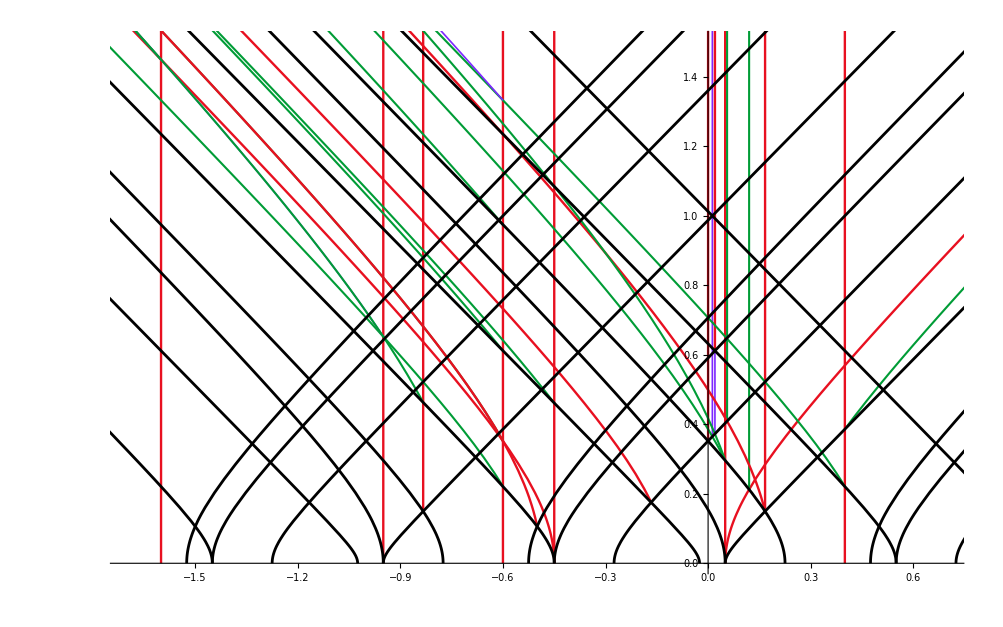

```mathematica
With[{psi=0, m=-1/10},Module[{rays,t0},
rays1=Table[
t0=If[FreeQ[#, Complex], #, 0]&@XYTost[ray[[2]], psi, m][[2]];
Tooltip[Style[{Rays[ray[[1]], t+t0, psi, m], t+t0}, Lookup[RayStyleMap,ray[[7]],Directive[Black,Thickness[.002]]]], ChernToCh[ray[[1]]]],
{ray,Complement[ExpandedRays, InitialRays]}];
rays2=Table[
t0=0;
Tooltip[Style[{Rays[ray[[1]], t+t0, psi, m], t+t0}, Lookup[RayStyleMap,ray[[7]],Directive[Black,Thickness[.002]]]], ChernToCh[ray[[1]]]],
{ray,InitialRays}];

ParametricPlot[Evaluate[Join[rays1,rays2]], {t, 0, 2},
PlotRange->{{-1.7, .7}, {0,1.5}},
AspectRatio->2/3
]]]
```

```mathematica
ExampleRays
```

{{{-1,-2,-1,-3/2},{83/120,-223/120},0,0,0,0,0},{{0,1,0,0},{1/20,0},3,12,1,1,1},{{0,1,1,1/2},{1/6,0},3,18,1,1,1},{{2,1,1,-1/2},{-1/6,0},4,21,3,1,1},{{1,0,0,-1},{-1/2,-1},9,22,1,2,1},{{0,0,1,1/2},{2/5,-7/10},11,18,1,1,1},{{0,4,2,0},{1/50,3/2},15,24,1,1,1},{{0,2,2,0},{0,1/2},18,21,1,1,1},{{-1,0,1,1/2},{2/5,0},3,139,1,1,2},{{1,0,1,-1/2},{-3/5,0},4,123,1,1,2},{{2,1,0,-1},{-9/20,0},4,164,2,1,2},{{0,2,1,1/2},{3/25,7/50},18,64,1,1,2},{{1,1,2,0},{-3/5,23/10},18,123,1,1,2},{{0,3,3,1/2},{1/18,2/3},21,66,1,1,2},{{1,0,0,-2},{-5/6,-2},22,32,1,1,2},{{1,2,2,2},{2/5,-2/5},24,139,1,1,2},{{1,0,0,-2},{-8/5,-2},112,165,1,1,2},{{1,0,0,-1},{-3/5,-1},123,165,1,1,2},{{0,3,2,0},{1/80,43/80},21,520,1,1,3},{{0,4,2,0},{1/50,14/25},21,521,1,1,3},{{1,0,0,-2},{-19/20,-2},28,617,1,1,3},{{1,2,3,3/2},{-3/5,28/5},123,645,1,1,3}}

```mathematica
MinMax@ExampleRays[[All,2,2]]//N
```

{-2.,5.6}

```mathematica
XYTost[#,0,-1/10]&/@ExampleRays[[All,2]]//N
Max@Select[%[[All,2]], FreeQ[#,Complex]&]
```

{{0.691667,0.+0.0687184 ⅈ},{0.05,0.},{0.166667,0.149536},{-0.166667,0.175198},{-0.5,0.106066},{0.4,0.+0.162019 ⅈ},{0.02,0.611269},{0.,0.351781},{0.4,0.385681},{-0.6,0.611351},{-0.45,0.460977},{0.12,0.212485},{-0.6,0.974038},{0.0555556,0.408796},{-0.833333,0.462631},{0.4,0.220794},{-1.6,1.44871},{-0.6,0.351781},{0.0125,0.364649},{0.02,0.372357},{-0.95,0.65192},{-0.6,1.33182}}

1.44871

```mathematica
Expand@XYParabolaY[x,mu,0,0]
```

mu^2/2-mu x-4 x^2

## Examples at m = 1/10

Adding 233 rays,

Adding 1226 rays,

Adding 1357 rays,

Adding 202 rays,

Adding 3 rays,

3053 in total.

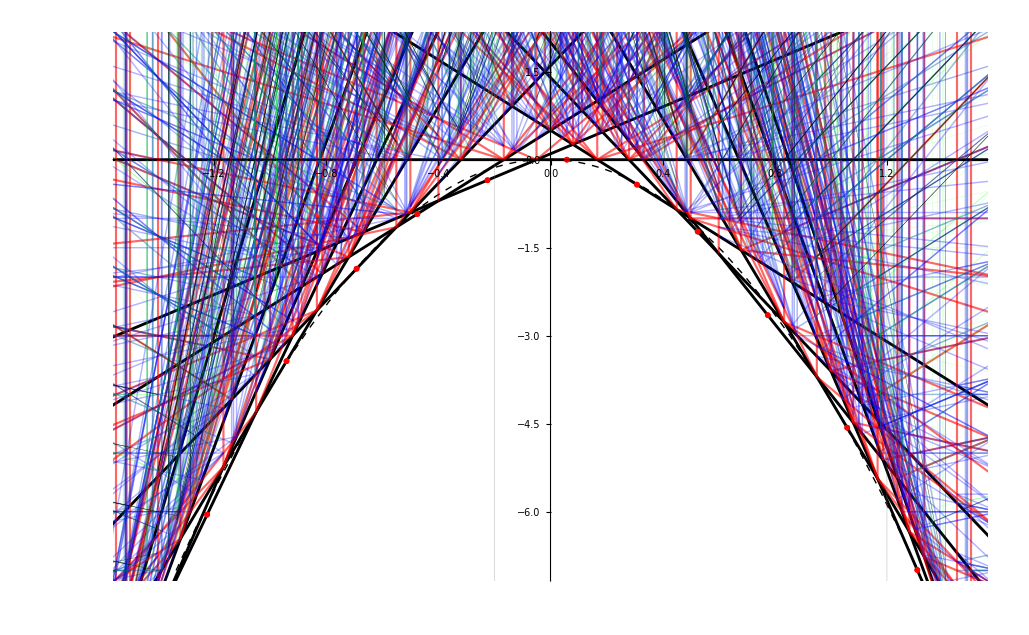

```mathematica
With[{mu=1/10, L=4,len=20},
InitialRaysp=InitialRaysFromColl[CollInitial[[1]]/.repCh, -2,2,mu];
ListRaysp=ConstructLVDiagramOpt[13,4,mu,InitialRaysp];

Show[
Plot[XYParabolaY[x,mu,0,0],{x,-2,2},
PlotRange->{{-1.5,1.5},{-7,2}},
PlotStyle->Directive[Dashed,Thick,Black],
GridLines->{{-0.2,1.2},None}
],
(*Graphics[{Opacity[.25],ConstructDomain[#, mu,L]&/@CollPlotData}],*)
Graphics[{
Tooltip[XYRaySegment[#,mu,len,RayStyleMap], #[[1]]]&/@ListRaysp,    (*rays*)
PointSize[.004],Red,
Point[#[[2]]&/@InitialRaysp]                   (*initial positions*)
}]
]
]
```

```mathematica
indexTablep=Table[
temp=LVTreesFromListRays[ListRaysp,gam,1/10];
{ToHC[gam],gam, Column[ChernToCh[temp]], Column[ChernToCh[temp]/.{Ch[p_,q_]:>ChHC[p,-p+q]}], Series[Total[ScattIndexImproved[temp, y]], {y,Infinity,100}]},
 {gam, ObjectsToCheck}];
```

```mathematica
Grid[Prepend[indexTablep, {"gam in HC", "gam in FB", "Trees", "Trees in HC", "Improved Index"}],Frame->All]
```

gam in HC | gam in FB | Trees | Trees in HC | Improved Index
{0,0,1,1/2} | {0,0,1,1/2} | {Ch[2,1][1],Ch[2,2]} | {ChHC[2,-1][1],ChHC[2,0]} | 1
{0,1,-1,0} | {0,1,0,0} | {Ch[0,0],Ch[-1,0][1]} | {ChHC[0,0],ChHC[-1,1][1]} | -y-1/y+O[1/y]^101
{0,1,0,1/2} | {0,1,1,1/2} | {Ch[0,0][1],Ch[1,1]} | {ChHC[0,0][1],ChHC[1,0]} | y^2+1+(1/y)^2+O[1/y]^101
{0,2,-1,1/2} | {0,2,1,1/2} | {Ch[1,1],Ch[-1,0][1]} | {ChHC[1,0],ChHC[-1,1][1]} | y^4+y^2+1+(1/y)^2+(1/y)^4+O[1/y]^101
{0,2,0,0} | {0,2,2,0} | {Ch[1,1],Ch[-1,-1][1]} | {ChHC[1,0],ChHC[-1,0][1]} | -y^5-y^3-y-1/y-(1/y)^3-(1/y)^5+O[1/y]^101
{0,3,-1,0} | {0,3,2,0} | {Ch[1,1],{Ch[-1,-1][1],{Ch[0,0],Ch[-1,0][1]}}} | {ChHC[1,0],{ChHC[-1,0][1],{ChHC[0,0],ChHC[-1,1][1]}}} | -y^9-3 y^7-4 y^5-4 y^3-4 y-4/y-4/y^3-4/y^5-3/y^7-(1/y)^9+O[1/y]^101
{0,3,0,1/2} | {0,3,3,1/2} | {Ch[-1,-1][1],{Ch[0,0][1],2 Ch[1,1]}} | {ChHC[-1,0][1],{ChHC[0,0][1],2 ChHC[1,0]}} | y^10+2 y^8+3 y^6+3 y^4+3 y^2+3+3/y^2+3/y^4+3/y^6+2/y^8+(1/y)^10+O[1/y]^101
{0,4,-2,0} | {0,4,2,0} | {Ch[-2,-1][1],Ch[2,1]}
{Ch[1,1],{Ch[-1,-1][1],{2 Ch[0,0],2 Ch[-1,0][1]}}} | {ChHC[-2,1][1],ChHC[2,-1]}
{ChHC[1,0],{ChHC[-1,0][1],{2 ChHC[0,0],2 ChHC[-1,1][1]}}} | -y^13-3 y^11-8 y^9-10 y^7-11 y^5-11 y^3-11 y-11/y-11/y^3-11/y^5-10/y^7-8/y^9-3/y^11-(1/y)^13+O[1/y]^101
{1,2,0,2} | {1,2,2,2} | Ch[2,2] | ChHC[2,0] | 1
{1,0,1,-1/2} | {1,0,1,-1/2} | {Ch[0,0],{Ch[-1,-1][1],Ch[-1,0]}} | {ChHC[0,0],{ChHC[-1,0][1],ChHC[-1,1]}} | 1
{1,1,1,0} | {1,1,2,0} | {Ch[1,1],{Ch[-1,-1][1],Ch[-1,0]}} | {ChHC[1,0],{ChHC[-1,0][1],ChHC[-1,1]}} | 1
{1,2,1,3/2} | {1,2,3,3/2} | {Ch[2,2],{Ch[-1,-1][1],Ch[-1,0]}} | {ChHC[2,0],{ChHC[-1,0][1],ChHC[-1,1]}} | 1
{-1,0,1,1/2} | {-1,0,1,1/2} | {Ch[0,0][1],{Ch[2,1][1],Ch[2,2]}} | {ChHC[0,0][1],{ChHC[2,-1][1],ChHC[2,0]}} | 1
{-1,-2,1,-3/2} | {-1,-2,-1,-3/2} | Ch[2,1][1] | ChHC[2,-1][1] | 1
{1,0,0,-1} | {1,0,0,-1} | {Ch[-1,0],{Ch[-2,-1][1],Ch[-1,-1]}} | {ChHC[-1,1],{ChHC[-2,1][1],ChHC[-1,0]}} | y^2+2+(1/y)^2+O[1/y]^101
{1,0,0,-2} | {1,0,0,-2} | {Ch[-1,0],{Ch[-3,-2],Ch[-4,-2][1]}}
{Ch[-1,-1],{Ch[-3,-2][1],Ch[-2,-1]}}
{{Ch[-2,-1][1],2 Ch[-1,-1]},{Ch[-4,-3][1],Ch[-4,-2]}} | {ChHC[-1,1],{ChHC[-3,1],ChHC[-4,2][1]}}
{ChHC[-1,0],{ChHC[-3,1][1],ChHC[-2,1]}}
{{ChHC[-2,1][1],2 ChHC[-1,0]},{ChHC[-4,1][1],ChHC[-4,2]}} | y^4+3 y^2+6+3/y^2+(1/y)^4+O[1/y]^101
{2,1,0,-1/2} | {2,1,1,-1/2} | {3 Ch[0,0],Ch[-1,-1][1]} | {3 ChHC[0,0],ChHC[-1,0][1]} | 1
{2,1,-1,-1} | {2,1,0,-1} | {2 Ch[0,0],{Ch[-2,-1][1],Ch[-1,-1]}} | {2 ChHC[0,0],{ChHC[-2,1][1],ChHC[-1,0]}} | -y-1/y+O[1/y]^101

## Examples at m = 4/10

Adding 233 rays,

Adding 1221 rays,

Adding 1301 rays,

Adding 197 rays,

Adding 3 rays,

2987 in total.

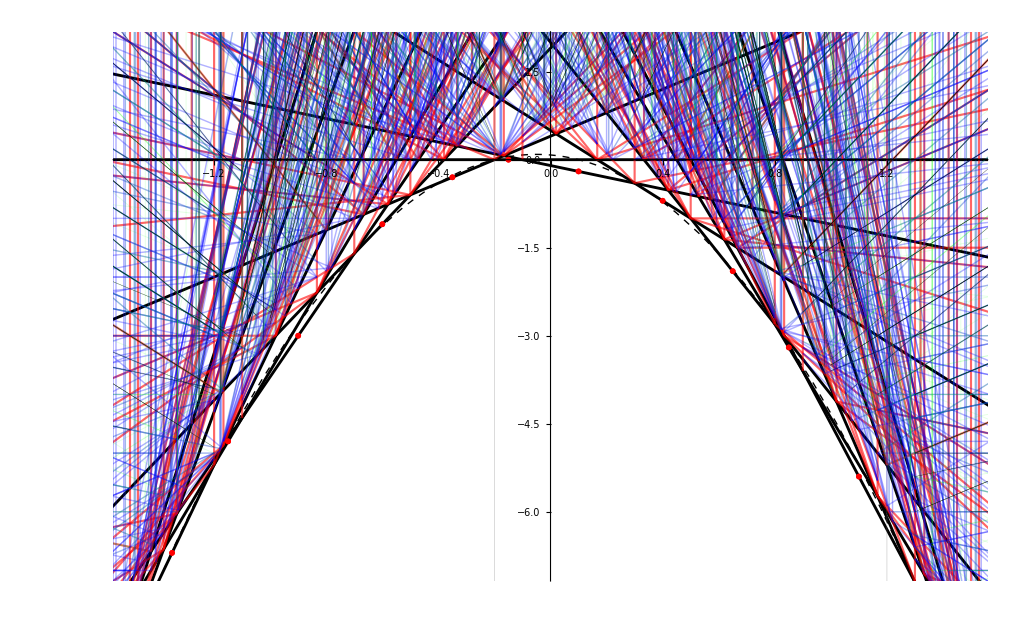

```mathematica
With[{mu=4/10, L=4,len=20},
InitialRayspp=InitialRaysFromColl[CollInitial[[2]]/.repCh, -2,2,mu];
ListRayspp=ConstructLVDiagramOpt[13,4,mu,InitialRayspp];

Show[
Plot[XYParabolaY[x,mu,0,0],{x,-2,2},
PlotRange->{{-1.5,1.5},{-7,2}},
PlotStyle->Directive[Dashed,Thick,Black],
GridLines->{{-0.2,1.2},None}
],
(*Graphics[{Opacity[.25],ConstructDomain[#, mu,L]&/@CollPlotData}],*)
Graphics[{
Tooltip[XYRaySegment[#,mu,len,RayStyleMap], #[[1]]]&/@ListRayspp,    (*rays*)
PointSize[.004],Red,
Point[#[[2]]&/@InitialRayspp]                   (*initial positions*)
}]
]
]
```

```mathematica
indexTablepp=Table[
temp=LVTreesFromListRays[ListRayspp,gam,4/10];
{ToHC[gam],gam, Column[ChernToCh[temp]], Column[ChernToCh[temp]/.{Ch[p_,q_]:>ChHC[p,-p+q]}], Series[Total[ScattIndexImproved[temp, y]], {y,Infinity,100}]},
 {gam, ObjectsToCheck}];
```

```mathematica
Grid[Prepend[indexTablepp, {"gam in HC", "gam in FB", "Trees", "Trees in HC", "Improved Index"}],Frame->All]
```

gam in HC | gam in FB | Trees | Trees in HC | Improved Index
{0,0,1,1/2} | {0,0,1,1/2} | {Ch[3,2][1],Ch[3,3]} | {ChHC[3,-1][1],ChHC[3,0]} | 1
{0,1,-1,0} | {0,1,0,0} | {Ch[0,0],Ch[-1,0][1]} | {ChHC[0,0],ChHC[-1,1][1]} | -y-1/y+O[1/y]^101
{0,1,0,1/2} | {0,1,1,1/2} | {Ch[0,0][1],Ch[1,1]} | {ChHC[0,0][1],ChHC[1,0]} | y^2+1+(1/y)^2+O[1/y]^101
{0,2,-1,1/2} | {0,2,1,1/2} | {Ch[1,1],Ch[-1,0][1]} | {ChHC[1,0],ChHC[-1,1][1]} | y^4+y^2+1+(1/y)^2+(1/y)^4+O[1/y]^101
{0,2,0,0} | {0,2,2,0} | {Ch[1,1],{Ch[-1,0][1],{Ch[0,0][1],Ch[0,1]}}} | {ChHC[1,0],{ChHC[-1,1][1],{ChHC[0,0][1],ChHC[0,1]}}} | -y^5-y^3-y-1/y-(1/y)^3-(1/y)^5+O[1/y]^101
{0,3,-1,0} | {0,3,2,0} | {Ch[1,1],{Ch[0,1],2 Ch[-1,0][1]}}
{Ch[1,1],{{Ch[0,0][1],Ch[0,1]},{Ch[0,0],2 Ch[-1,0][1]}}} | {ChHC[1,0],{ChHC[0,1],2 ChHC[-1,1][1]}}
{ChHC[1,0],{{ChHC[0,0][1],ChHC[0,1]},{ChHC[0,0],2 ChHC[-1,1][1]}}} | -y^9-3 y^7-4 y^5-4 y^3-4 y-4/y-4/y^3-4/y^5-3/y^7-(1/y)^9+O[1/y]^101
{0,3,0,1/2} | {0,3,3,1/2} | {{Ch[0,0][1],2 Ch[1,1]},{Ch[-1,0][1],{Ch[0,0][1],Ch[0,1]}}} | {{ChHC[0,0][1],2 ChHC[1,0]},{ChHC[-1,1][1],{ChHC[0,0][1],ChHC[0,1]}}} | y^10+2 y^8+3 y^6+3 y^4+3 y^2+3+3/y^2+3/y^4+3/y^6+2/y^8+(1/y)^10+O[1/y]^101
{0,4,-2,0} | {0,4,2,0} | {Ch[-2,-1][1],{Ch[0,1][1],2 Ch[1,1]}}
{Ch[1,1],{{Ch[0,0],2 Ch[-1,0][1]},{Ch[0,1],Ch[-1,0][1]}}} | {ChHC[-2,1][1],{ChHC[0,1][1],2 ChHC[1,0]}}
{ChHC[1,0],{{ChHC[0,0],2 ChHC[-1,1][1]},{ChHC[0,1],ChHC[-1,1][1]}}} | -y^13-3 y^11-7 y^9-9 y^7-10 y^5-10 y^3-10 y-10/y-10/y^3-10/y^5-9/y^7-7/y^9-3/y^11-(1/y)^13+O[1/y]^101
{1,2,0,2} | {1,2,2,2} | Ch[2,2] | ChHC[2,0] | 1
{1,0,1,-1/2} | {1,0,1,-1/2} | Ch[0,1] | ChHC[0,1] | 1
{1,1,1,0} | {1,1,2,0} | {Ch[1,1],{Ch[0,0][1],Ch[0,1]}} | {ChHC[1,0],{ChHC[0,0][1],ChHC[0,1]}} | 1
{1,2,1,3/2} | {1,2,3,3/2} | {Ch[2,2],{Ch[0,0][1],Ch[0,1]}} | {ChHC[2,0],{ChHC[0,0][1],ChHC[0,1]}} | 1
{-1,0,1,1/2} | {-1,0,1,1/2} | {Ch[0,0][1],{Ch[3,2][1],Ch[3,3]}} | {ChHC[0,0][1],{ChHC[3,-1][1],ChHC[3,0]}} | 1
{-1,-2,1,-3/2} | {-1,-2,-1,-3/2} | {Ch[2,2][1],{Ch[3,2][1],Ch[3,3]}} | {ChHC[2,0][1],{ChHC[3,-1][1],ChHC[3,0]}} | 1
{1,0,0,-1} | {1,0,0,-1} | {Ch[-1,0],{Ch[-3,-1][1],Ch[-2,-1]}} | {ChHC[-1,1],{ChHC[-3,2][1],ChHC[-2,1]}} | y^2+2+(1/y)^2+O[1/y]^101
{1,0,0,-2} | {1,0,0,-2} | {Ch[-1,0],{Ch[-3,-2],Ch[-4,-2][1]}}
{{Ch[-3,-2][1],Ch[-2,-1]},{Ch[-3,-1][1],2 Ch[-2,-1]}} | {ChHC[-1,1],{ChHC[-3,1],ChHC[-4,2][1]}}
{{ChHC[-3,1][1],ChHC[-2,1]},{ChHC[-3,2][1],2 ChHC[-2,1]}} | y^4+3 y^2+5+3/y^2+(1/y)^4+O[1/y]^101
{2,1,0,-1/2} | {2,1,1,-1/2} | {Ch[0,1],{2 Ch[0,0],Ch[-1,0][1]}} | {ChHC[0,1],{2 ChHC[0,0],ChHC[-1,1][1]}} | 1
{2,1,-1,-1} | {2,1,0,-1} | {2 Ch[0,0],{Ch[-3,-1][1],Ch[-2,-1]}} | {2 ChHC[0,0],{ChHC[-3,2][1],ChHC[-2,1]}} | -y-1/y+O[1/y]^101